# Math 223: Homework 8

Hardeep Bassi

04/07/2023

## Problem 1

Find the asymptotic behavior of , as  up to terms involving 
From lecture, we know that integration by parts works well on 
when is monotonic on the given interval. Since , we satisfy this criterion, hence we obtain:
. Using this formula for the first two terms yields:
. To check this approximation we see:

```mathematica
approx[x_] = (-I*(2+Sin[2])*E^(2*I*x))/x + (E^(2*I*x)*(Cos[2]+1))/x^2 - 2/x^2
```

-2/x^2+(ⅇ^(2 ⅈ x) (1+Cos[2]))/x^2-(ⅈ ⅇ^(2 ⅈ x) (2+Sin[2]))/x

```mathematica
exact[x_] = Integrate[(Sin[t] + t) * E^(I*x*t), {t,0,2}]
```

(-1+ⅇ^(2 ⅈ x) (1-2 ⅈ x))/x^2+(-1+ⅇ^(2 ⅈ x) (Cos[2]-ⅈ x Sin[2]))/(-1+x^2)

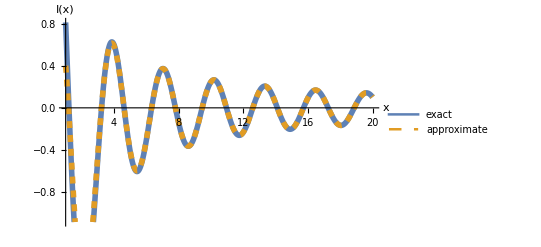

```mathematica
Plot[{Re[exact[x]], Re[approx[x]]},{x,1,20},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact", "approximate"}]
```

We see agreement between the exact and the approximate solution as , so we appear to be good to go.

## Problem 2

Restate the problem here and follow up with any computations or explanations.

## Problem 3

Restate the problem here and follow up with any computations or explanations.